```mathematica
Table[x,4]
```

{x,x,x,x}

```mathematica
Table[x,3,4]
```

{{x,x,x,x},{x,x,x,x},{x,x,x,x}}

```mathematica
Grid[Table[x,3,4]]
```

x | x | x | x
x | x | x | x
x | x | x | x

```mathematica
Grid[Table[i,{i,1,3},{j,1,4}]]
```

1 | 1 | 1 | 1
2 | 2 | 2 | 2
3 | 3 | 3 | 3

```mathematica
Grid[Table[j,{i,1,3},{j,1,4}]]
```

1 | 2 | 3 | 4
1 | 2 | 3 | 4
1 | 2 | 3 | 4

```mathematica
Grid[Table[i*j,{i,1,5},{j,1,5}]]
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

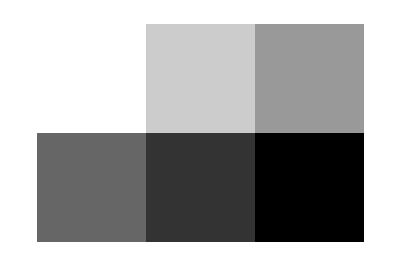

```mathematica
ArrayPlot[{{0,1,2},{3,4,5}}]
```

```mathematica
ArrayPlot[Table[RandomInteger[10],30,30]]
```

-Graphics-

```mathematica
ArrayPlot[Table[Max[j-i,0],{i,10},{j,10}]]
```

-Graphics-

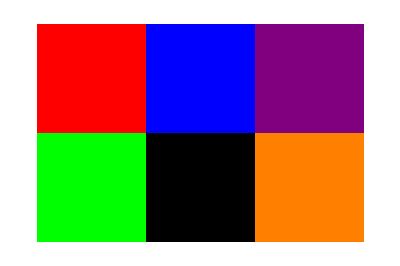

```mathematica
ArrayPlot[{{Red, Blue, Purple},{Green, Black,Orange}}]
```

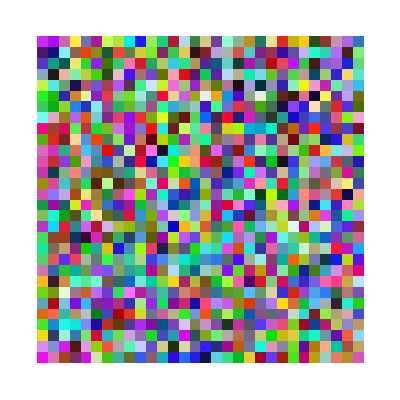

```mathematica
ArrayPlot[Table[RandomColor[],30,30]]
```

```mathematica
Rasterize["W"]
```

-Graphics-

```mathematica
Binarize[Rasterize["W"]]
```

-Graphics-

```mathematica
ImageData[Binarize[Rasterize["W"]]]
```

{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{0,1,1,1,1,1,0,0},{0,0,1,1,1,1,0,0},{0,0,1,0,0,1,0,1},{0,0,1,0,0,1,0,1},{1,0,1,0,0,1,0,1},{1,0,1,0,0,1,0,1},{1,0,0,1,0,0,0,1},{1,0,0,1,1,0,0,1},{1,0,0,1,1,0,0,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}}

```mathematica
ArrayPlot[ImageData[Binarize[Rasterize["W"]]]]
```

-Graphics-

```mathematica
1-{1,0,0}
```

{0,1,1}

```mathematica
1-ImageData[Binarize[Rasterize["W"]]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,1},{1,1,0,0,0,0,1,1},{1,1,0,1,1,0,1,0},{1,1,0,1,1,0,1,0},{0,1,0,1,1,0,1,0},{0,1,0,1,1,0,1,0},{0,1,1,0,1,1,1,0},{0,1,1,0,0,1,1,0},{0,1,1,0,0,1,1,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
ArrayPlot[1-ImageData[Binarize[Rasterize["W"]]]]
```

-Graphics-

Vocabulary
	Table[x,4,5]	
	Grid[array]
	ArrayPlot[array]
	ImagePlot[array]
    ---------------------------------------------------------------------

```mathematica
Grid[Table[StringJoin[FromLetterNumber[i],FromLetterNumber[j]],{i,1,7},{j,1,7}]]
```

aa | ab | ac | ad | ae | af | ag
ba | bb | bc | bd | be | bf | bg
ca | cb | cc | cd | ce | cf | cg
da | db | dc | dd | de | df | dg
ea | eb | ec | ed | ee | ef | eg
fa | fb | fc | fd | fe | ff | fg
ga | gb | gc | gd | ge | gf | gg